```mathematica
SetDirectory[NotebookDirectory[]];
Print[NotebookDirectory[]];
ClearAll[ABC];
Get["ABCInterpolator.wl"]
```

/Users/amigdal/Documents/Wolfram/

```mathematica
ABC[0.25]
```

{1.14837,0.00261698,0.0584979}

```mathematica
(* ==========================================================*)(*BLAZING FAST PRE-COMPILED DF (SAFE FOR PARALLELIZATION)*)(* ==========================================================*)ClearAll[DF,ZI0,ZI1,ZI2,DFIntegrand];

(*1. Pre-compile analytical derivatives (NO calculus inside the loop!)*)
ZI0[p_,A_,B_,C_]=20 C^(-1+p) (A C-B p);
ZI1[p_,A_,B_,C_]=20 C^(-1+p) (-B+(A C-B p) Log[C]);
ZI2[p_,A_,B_,C_]=20 C^(-1+p) Log[C] (-2 B+(A C-B p) Log[C]);

(*2. Strictly numerical integrand helper with explicit dummy variable xVar*)
DFIntegrand[p_?NumericQ,n_Integer,xVar_?NumericQ]:=Block[{A,B,C,Zval},{A,B,C}=ABC[xVar];
Zval=Switch[n,0,ZI0[p,A,B,C],1,ZI1[p,A,B,C],2,ZI2[p,A,B,C]];
(1-xVar)*Zval];

(*3. The exact numerical integration wrapper*)
DF[p_?NumericQ,n_Integer]:=Quiet[NIntegrate[DFIntegrand[p,n,xVar],{xVar,Δ1,Δ2},MaxRecursion->30,(*Allows deep zooming into sharp complex spikes*)Method->"GlobalAdaptive"],{NIntegrate::slwcon,NIntegrate::ncvb,NIntegrate::eincr}];

(*Ensure the parallel kernels know these definitions for the later steps*)
DF[-3,0]
```

24057.

```mathematica
ClearAll[OddLog,OddLog1,OddLog2,S,S1,S2];
UseOdd= True;
OddLog[p_?NumericQ]:=If[TrueQ[UseOdd],-Log[1-2^(-(p+17/2))],0];OddLog1[p_?NumericQ]:=If[TrueQ[UseOdd],-Log[2] 2^(-(p+17/2))/(1-2^(-(p+17/2))),0];OddLog2[p_?NumericQ]:=If[TrueQ[UseOdd],Log[2]^2 2^(-(p+17/2))/(1-2^(-(p+17/2)))^2,0];
```

```mathematica
S2[p_]:=DF[p,2]/DF[p,0]-(DF[p,1]/DF[p,0])^2 + PolyGamma[1,-p]+Zeta''[p+15/2]/Zeta[p+15/2]-(Zeta'[p+15/2]/Zeta[p+15/2])^2-Zeta''[p+17/2]/Zeta[p+17/2]+(Zeta'[p+17/2]/Zeta[p+17/2])^2+4/(2 p+7)^2+4/(2 p+17)^2 +OddLog2[p];
```

```mathematica
S1[p_]:=DF[p,1]/DF[p,0]-PolyGamma[0,-p]+Zeta'[p+15/2]/Zeta[p+15/2]-Zeta'[p+17/2]/Zeta[p+17/2]-2/(2 p+7)-2/(2 p+17) +OddLog1[p];
```

```mathematica
(*Plot[-S1[p], {p, -3.5,0.}]*)
```

$Aborted

```mathematica
S[p_]:=Log[DF[p,0]]+LogGamma[-p]+Log[Zeta[p+15/2]]- Log[Zeta[p+17/2]]-Log[2 p+7]-Log[2 p+17] +OddLog[p];
```

```mathematica
sp1data =ParallelTable[{-S1[p],p}, {p, -3.499,0., 0.01}];
```

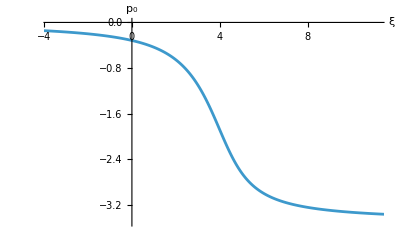

```mathematica
ListLinePlot[sp1data, AxesLabel->{ξ, Subscript[p,0]}]
```

```mathematica
Integrate[Sin[k r]/(k r) k^p, {k,0,Infinity}, Assumptions->{p > -1, r >0}]
```

ConditionalExpression[r^(-1-p) Gamma[p] Sin[(p π)/2], p<1]

```mathematica
ZZ[q_] := FullSimplify[(Gamma[p] Sin[(p π)/2]DF[p,0]Gamma[-p]Zeta[p+15/2]/ Zeta[p+17/2]/(2 p+7)/(2 p+17) /(1-2^(-(p+17/2))))/.p->-1-q,q <0]
```

```mathematica
Factor[(75+35 q-36 q^2+4 q^3)]
```

(1+q) (-15+2 q) (-5+2 q)

```mathematica
ZR[q_]:= ZZ[q]/.(75+35 q-36 q^2+4 q^3)->(1+q) (-15+2 q) (-5+2 q)
```

```mathematica
ZR[q]
```

-(64 √2 π Csc[(π q)/2] DF[-1-q,0] Zeta[13/2-q])/((128 √2-2^q) (1+q) (-15+2 q) (-5+2 q) Zeta[15/2-q])

```mathematica
fp =FunctionPoles[{-(64 √2 π Csc[(π q)/2]  Zeta[13/2-q])/((128 √2-2^q) (1+q) (-15+2 q) (-5+2 q) Zeta[15/2-q]),-30<Re[q]<0},q]
```

{{-28,1},{-26,1},{-24,1},{-22,1},{-20,1},{-18,1},{-16,1},{-14,1},{-12,1},{-10,1},{-8,1},{-6,1},{-4,1},{-2,1},{-1,1}}

```mathematica
First/@fp
```

{-28,-26,-24,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,-1}

```mathematica
qvals =Flatten[Table[x+ I y,{x, -1,0, 0.1},{y, 0,10,0.1}]];
```

```mathematica
df0values = 
ParallelTable[
Module[{q=qvals[[n]]},
{{Re[q], Im[q]},Re[Log[DF[-1-q,0]]]}],{n, Length[qvals]}];
```

```mathematica
df0lm =LinearModelFit[{#[[1,1]],#[[1,2]],#[[2]]}& /@df0values,{1,x,y},{x,y}]
```

FittedModel[…]

```mathematica
df0interp = Interpolation[df0values];
```

```mathematica
df0approx[p_] := 
Block[{x0,x1,y0,y1},
{{x0,x1},{y0,y1}} =df0interp["Domain"];  
If[x0<=Re[p] <= x1 && y0<=Im[p] <= y1,df0interp[Re[p],Im[p]],df0lm[Re[p],Im[p]]]
];
```

```mathematica
Plot3D[df0approx[x+ I y],{x, -1,0},{y, 10,60}]
```

-Graphics3D-

```mathematica
SInterp[q_]:=df0approx[q]+Log[-(64 √2 π Csc[(π q)/2]  Zeta[13/2-q])/((128 √2-2^q) (1+q) (-15+2 q) (-5+2 q) Zeta[15/2-q])];
```

```mathematica
SInterpLM[q_]:=df0lm[Re[q],Im[q]] +Log[-(64 √2 π Csc[(π q)/2]  Zeta[13/2-q])/((128 √2-2^q) (1+q) (-15+2 q) (-5+2 q) Zeta[15/2-q])];
```

```mathematica
Plot3D[Re[SInterpLM[x+ I y]],{x, -1,0},{y, 10,60}]
```

-Graphics3D-

```mathematica
df1values = 
ParallelTable[
Module[{q=qvals[[n]],f0,f1},
f0=DF[-1-q,0];f1=DF[-1-q,1];
{{Re[q], Im[q]},f1/f0}],{n, Length[qvals]}];
```

```mathematica
df1Mean =Mean[#[[2]] & /@ df1values]
```

-2.86581+0.00164606 ⅈ

```mathematica
ListPlot3D[{#[[1,1]],#[[1,2]],Re[#[[2]]]}& /@ df1values]
```

-Graphics3D-

```mathematica
df1interp = Interpolation[df1values];
```

```mathematica
df1approx[p_] := 
Block[{x0,x1,y0,y1},
{{x0,x1},{y0,y1}} =df1interp["Domain"];  
If[x0<=Re[p] <= x1 && y0<=Im[p] <= y1,df1interp[Re[p],Im[p]],df1Mean]
];
```

```mathematica
df1approx[-0.15]
```

-2.86932+0. ⅈ

```mathematica
Plot3D[ReIm[df1approx[x+ I y]],{x, -10,0},{y, 0,10}]
```

-Graphics3D-

```mathematica
ClearAll[S1Analytic];
```

```mathematica
S1Analytic[q_] =D[Log[-(64 √2 π Csc[(π q)/2]  Zeta[13/2-q])/((128 √2-2^q) (1+q) (-15+2 q) (-5+2 q) Zeta[15/2-q])],q]//Simplify
```

-1/(2 (1+q) (-15+2 q) (-5+2 q))(π (75+35 q-36 q^2+4 q^3) Cot[(π q)/2]+1/(128 √2-2^q)2 (72 (-128 √2+2^q) q-35 2^q q Log[2]-2^(2+q) q^3 Log[2]+5 (896 √2-7 2^q-15 2^q Log[2])+12 q^2 (128 √2-2^q+2^q Log[8]))+(2 (75+35 q-36 q^2+4 q^3) Zeta'[13/2-q])/Zeta[13/2-q]-(2 (75+35 q-36 q^2+4 q^3) Zeta'[15/2-q])/Zeta[15/2-q])

```mathematica
S1R[q_] := -DF[-1-q,1]/DF[-1-q,0]  + S1Analytic[q];
```

```mathematica
S2Analytic[q_] = D[S1Analytic[q],q]//Simplify
```

1/(2 (5-2 q)^2 (15-2 q)^2 (1+q)^2)(2 (1+q) (-15+2 q) (π (75+35 q-36 q^2+4 q^3) Cot[(π q)/2]+1/(128 √2-2^q)2 (72 (-128 √2+2^q) q-35 2^q q Log[2]-2^(2+q) q^3 Log[2]+5 (896 √2-7 2^q-15 2^q Log[2])+12 q^2 (128 √2-2^q+2^q Log[8]))+(2 (75+35 q-36 q^2+4 q^3) Zeta'[13/2-q])/Zeta[13/2-q]-(2 (75+35 q-36 q^2+4 q^3) Zeta'[15/2-q])/Zeta[15/2-q])+2 (1+q) (-5+2 q) (π (75+35 q-36 q^2+4 q^3) Cot[(π q)/2]+1/(128 √2-2^q)2 (72 (-128 √2+2^q) q-35 2^q q Log[2]-2^(2+q) q^3 Log[2]+5 (896 √2-7 2^q-15 2^q Log[2])+12 q^2 (128 √2-2^q+2^q Log[8]))+(2 (75+35 q-36 q^2+4 q^3) Zeta'[13/2-q])/Zeta[13/2-q]-(2 (75+35 q-36 q^2+4 q^3) Zeta'[15/2-q])/Zeta[15/2-q])+(-15+2 q) (-5+2 q) (π (75+35 q-36 q^2+4 q^3) Cot[(π q)/2]+1/(128 √2-2^q)2 (72 (-128 √2+2^q) q-35 2^q q Log[2]-2^(2+q) q^3 Log[2]+5 (896 √2-7 2^q-15 2^q Log[2])+12 q^2 (128 √2-2^q+2^q Log[8]))+(2 (75+35 q-36 q^2+4 q^3) Zeta'[13/2-q])/Zeta[13/2-q]-(2 (75+35 q-36 q^2+4 q^3) Zeta'[15/2-q])/Zeta[15/2-q])-(1+q) (-15+2 q) (-5+2 q) (π (35-72 q+12 q^2) Cot[(π q)/2]-1/2 π^2 (75+35 q-36 q^2+4 q^3) Csc[(π q)/2]^2-1/((-128 √2+2^q)^2)2^(1+q) Log[2] (35 (-128 √2+2^q)+75 2^q Log[2]+2^(2+q) q^3 Log[2]+q (9216 √2-9 2^(3+q)+35 2^q Log[2])-12 q^2 (128 √2-2^q+2^q Log[8]))+1/(128 √2-2^q)2 (72 (-128 √2+2^q)-35 2^(1+q) Log[2]-75 2^q Log[2]^2-35 2^q q Log[2]^2-2^(2+q) q^3 Log[2]^2+2^(2+q) q^2 (-2+Log[8]) Log[8]+8 q (384 √2-3 2^q+2^(1+q) Log[512]))+(2 (35-72 q+12 q^2) Zeta'[13/2-q])/Zeta[13/2-q]+(2 (75+35 q-36 q^2+4 q^3) Zeta'[13/2-q]^2)/Zeta[13/2-q]^2-(2 (35-72 q+12 q^2) Zeta'[15/2-q])/Zeta[15/2-q]-(2 (75+35 q-36 q^2+4 q^3) Zeta'[15/2-q]^2)/Zeta[15/2-q]^2-(2 (75+35 q-36 q^2+4 q^3) Zeta''[13/2-q])/Zeta[13/2-q]+(2 (75+35 q-36 q^2+4 q^3) Zeta''[15/2-q])/Zeta[15/2-q]))

```mathematica
S2R[q_] :=-DF[-1-q,2]/DF[-1-q,0]-(DF[-1-q,1]/DF[-1-q,0])^2 +S2Analytic[q];
```

```mathematica
S1Interp[q_?NumericQ] := df1approx[q] +S1Analytic[q];
```

```mathematica
S1R[-0.5]
```

2.90444

```mathematica
S2R[-0.5]
```

-7.40176

```mathematica
BuildThimble[p0_] := 
Module[{v0,eqs,path,xi,eps = 0.001,tMax= 15},
     v0 = I Sqrt[2/S2R[p0]];
xi = -S1R[p0];
eqs = {
p'[t] == -2t/(S1Interp[p[t]] + xi), 
p[eps] == p0 + eps*v0
};
Quiet[
        NDSolveValue[eqs, p, {t, eps, tMax},
          WorkingPrecision -> 20, AccuracyGoal -> 10, PrecisionGoal -> 10,
          Method -> "StiffnessSwitching", MaxSteps -> 300000],
        {NDSolveValue::precw, NDSolveValue::ndsz}
      ]
];
```

```mathematica
p0Values=Range[-0.99`20,0.`20,0.01`20];
```

```mathematica
thimbleData = ParallelTable[BuildThimble[p0Values[[n]]],{n, Length[p0Values]}];
```

Divide::infy: Infinite expression (2.×10^-17-«48» ⅈ)/0. encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Divide::infy: Infinite expression -(2.×10^-17+«46» ⅈ)/0. encountered.

Divide::infy: Infinite expression (4.×10^-17+0. ⅈ)/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression -145.50630144373866755+ComplexInfinity+ComplexInfinity encountered.

RowReduce::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

```mathematica
CountTrappedPoles[pFunc_, zZeros_] := Module[
  {vals, reVals, imVals, trapped = {}, crossings, tn},
  If[Head[pFunc] =!= InterpolatingFunction, Return[{}]];
  vals = pFunc["ValuesOnGrid"];
  reVals = Re[vals]; 
  imVals = Im[vals];
  Do[
    tn = zZeros[[n]];
    crossings = 0;
    Do[
      If[(imVals[[k]] <= tn && imVals[[k+1]] > tn) || (imVals[[k]] >= tn && imVals[[k+1]] < tn),
        Module[{w1, w2, reCross},
          w1 = Abs[imVals[[k+1]] - tn]; w2 = Abs[imVals[[k]] - tn];
          reCross = (w1 * reVals[[k]] + w2 * reVals[[k+1]]) / (w1 + w2);
          If[reCross < -8.0`50, crossings++];
        ]
      ];
    , {k, 1, Length[vals] - 1}];
    If[OddQ[crossings], AppendTo[trapped, n]];
  , {n, 1, Length[zZeros]}];
  trapped
];
Poles = Table[9 + I Im[N[ZetaZero[n],50]],{n,200}];
(* Imaginary parts of poles
□

 for crossing detection *)
zZeros = Im /@ Poles;
```

```mathematica
(* Detect incomplete thimble: solver stopped early, path didn't reach Re[p] = -8 *)
IsIncomplete[pFunc_] := Module[{tEnd, endVal},
  If[Head[pFunc] =!= InterpolatingFunction, Return[False]];
  tEnd = pFunc["Domain"][[1, 2]];
  endVal = pFunc[tEnd];
  tEnd < 14.9 && Re[endVal] > -8.0
];
```

```mathematica
(* Safety check *)
If[Length[p0Values] != Length[thimbleData],
  Print["Mismatch: ", Length[p0Values], " p0 values vs ", 
    Length[thimbleData], " thimbles. Adjusting..."];
  p0Values = p0Values[[;; Length[thimbleData]]];
];

(* Count trapped poles *)
nTrappedList = Table[
  Module[{pFunc = thimbleData[[k]]},
    Which[
      Head[pFunc] =!= InterpolatingFunction, -1,
      True, Length[CountTrappedPoles[pFunc, Im /@ Poles]]
    ]
  ],
  {k, Length[thimbleData]}
];

(* Build coordinate pairs explicitly — no Transpose needed *)
staircasePoints = Table[
  {N[-S1Interp[p0Values[[k]]]], nTrappedList[[k]]},
  {k, Length[p0Values]}
];

(* Staircase plot *)
ListStepPlot[staircasePoints,
  Frame -> True,
  FrameLabel -> {"Log[κ]", "Number of trapped poles"},
  PlotLabel -> "Stokes staircase: trapped poles vs. Log κ",
  PlotStyle -> {Thick, Blue},
  PlotRange -> {All, {-0.5, Max[nTrappedList] + 1}},
  GridLines -> Automatic,
  ImageSize -> 600,
  Epilog -> {Red, PointSize[0.012], Point[staircasePoints]}
]
```

-Graphics-

```mathematica
|
```

```mathematica
(* === Thimble Animation: ContourPlot background, 50 contours === *)

(* Ensure p0Values matches thimbleData *)
If[Length[p0Values] != Length[thimbleData],
  p0Values = p0Values[[;; Length[thimbleData]]];
];

(* Output folder *)
outputDir = FileNameJoin[{NotebookDirectory[], "ThimbleFrames"}];
If[!DirectoryQ[outputDir], CreateDirectory[outputDir]];

(* Full thimble: positive branch + conjugate negative branch *)
FullThimblePoints[p0_, pFunc_, nPts_: 600] := Module[{tMin, tMax, tvals, pts},
  If[Head[pFunc] =!= InterpolatingFunction, Return[{}]];
  {tMin, tMax} = pFunc["Domain"][[1]];
  tvals = Subdivide[tMin, tMax, nPts];
  pts = pFunc /@ tvals;
  Join[Reverse[Conjugate /@ pts], pts]
];
```

```mathematica
(* ============================================================ *)
(* FAST Thimble Animation: poles (red), zeros (green), thimble  *)
(* ============================================================ *)

(* === Complete Poles and Zeros of M(p) === *)

PolePts = Join[
  (* Riemann wall and conjugates *)
  Table[{-8., N[Im[ZetaZero[n]]]}, {n, 200}],
  Table[{-8., -N[Im[ZetaZero[n]]]}, {n, 200}],
  (* Real axis poles *)
  {{N[-7/2], 0.}},           (* from 1/(2p+7) *)
  {{N[-13/2], 0.}},          (* from Zeta[p+15/2] pole at s=1 *)
  {{N[-17/2], 0.}},          (* from 1/(2p+17) *)
  (* Trivial zeta poles: p = -17/2 - 2n *)
  Table[{N[-17/2 - 2 n], 0.}, {n, 1, 20}]
];

ZeroPts = Join[
  (* Nontrivial zeros and conjugates *)
  Table[{-7., N[Im[ZetaZero[n]]]}, {n, 200}],
  Table[{-7., -N[Im[ZetaZero[n]]]}, {n, 200}],
  (* Real axis zeros *)
  {{N[-15/2], 0.}},          (* from 1/Zeta[p+17/2] -> 0 at s=1 *)
  (* Trivial zeros of Zeta[p+15/2]: p = -15/2 - 2n *)
  Table[{N[-15/2 - 2 n], 0.}, {n, 1, 20}]
];

Print["Poles: ", Length[PolePts], "  Zeros: ", Length[ZeroPts]];

(* === Full thimble: upper branch + conjugate lower branch === *)
FullThimblePoints[p0_, pFunc_, nPts_: 600] := Module[{tMin, tMax, tvals, pts},
  If[Head[pFunc] =!= InterpolatingFunction, Return[{}]];
  {tMin, tMax} = pFunc["Domain"][[1]];
  tvals = Subdivide[tMin, tMax, nPts];
  pts = pFunc /@ tvals;
  Join[Reverse[Conjugate /@ pts], pts]
];

(* === FAST frame: square aspect ratio, fixed range === *)

PlotThimbleFrameFast[k_] := Module[
  {p0, pFunc, xi, fullPts, re, im, xmin, xmax, ymin, ymax,
   visPoles, visZeros, nTrapped},
  
  p0 = p0Values[[k]];
  pFunc = thimbleData[[k]];
  If[Head[pFunc] =!= InterpolatingFunction, Return[Nothing]];
  
  xi = -S1[p0];
  fullPts = FullThimblePoints[p0, pFunc];
  If[Length[fullPts] < 10, Return[Nothing]];
  
  re = Re[fullPts]; im = Im[fullPts];
  
  (* FIXED symmetric range: square frame *)
  xmin = Min[re] - 0.5;
  xmax = Max[re] + 0.5;
  (* Make y-range equal to x-range, centered at 0 *)
  ymax = (xmax - xmin)/2;
  ymin = -ymax;
  
  (* If thimble extends beyond, use thimble extent but keep square *)
  If[Max[Abs[im]] > ymax,
    ymax = Max[Abs[im]] + 0.5;
    ymin = -ymax;
    (* Now adjust x to match *)
    xmin = (xmin + xmax)/2 - ymax;
    xmax = (xmin + xmax)/2 + ymax;
  ];
  
  nTrapped = nTrappedList[[k]];
  
  visPoles = Select[PolePts, 
    xmin <= #[[1]] <= xmax && ymin <= #[[2]] <= ymax &];
  visZeros = Select[ZeroPts, 
    xmin <= #[[1]] <= xmax && ymin <= #[[2]] <= ymax &];
  
  Show[
    ListLinePlot[Transpose[{re, im}],
      PlotStyle -> {Thick, Blue},
      PlotRange -> {{xmin, xmax}, {ymin, ymax}},
      Frame -> True,
      FrameLabel -> {"Re(p)", "Im(p)"},
      AspectRatio -> 1,  (* SQUARE *)
      ImageSize -> 600
    ],
    Graphics[{
      (* Poles: red *)
      Red, PointSize[0.007], Point /@ visPoles,
      (* Zeros: green *)
      Darker[Green], PointSize[0.006], Point /@ visZeros,
      (* Saddle point: orange *)
      Orange, PointSize[0.02], Point[{Re[p0], 0}],
      (* Reference lines *)
      If[xmin < -8 < xmax,
        {Dashed, Red, Thickness[0.001], 
         Line[{{-8, ymin}, {-8, ymax}}]}, {}],
      If[xmin < -7 < xmax,
        {Dashed, Darker[Green], Thickness[0.001], 
         Line[{{-7, ymin}, {-7, ymax}}]}, {}]
    }],
    PlotLabel -> Style[
      Row[{"p0 = ", NumberForm[N[p0], {4, 2}],
        "   ξ = ", NumberForm[N[xi], {5, 3}],
        "   trapped = ", nTrapped}], 13, Bold],
    Background -> White
  ]
];


(* === Generate all frames === *)
outputDir = FileNameJoin[{NotebookDirectory[], "ThimbleFrames"}];
If[!DirectoryQ[outputDir], CreateDirectory[outputDir]];

Print["Generating frames..."];
thimblePlots = Table[
  If[Mod[k, 10] == 0, Print["Frame ", k, "/", Length[thimbleData]]];
  PlotThimbleFrameFast[k],
  {k, Length[thimbleData]}
] // DeleteCases[Nothing];
Print["Done. ", Length[thimblePlots], " frames generated."];

(* === Export frames to disk === *)
Print["Exporting frames to: ", outputDir];
Do[
  Export[
    FileNameJoin[{outputDir, 
      "frame_" <> IntegerString[k, 10, 3] <> ".png"}],
    thimblePlots[[k]], ImageResolution -> 150
  ],
  {k, Length[thimblePlots]}
];
Print["Exported ", Length[thimblePlots], " frames."];

(* === Interactive animation viewer === *)
(* AnimationRate goes in the VARIABLE spec, not as a top-level option *)
Manipulate[
  thimblePlots[[k]],
  {{k, 1, "frame"}, 1, Length[thimblePlots], 1, 
   AnimationRate -> 5, Appearance -> "Labeled"},
  AppearanceElements -> {"ProgressSlider", "PlayPauseButton",
    "StepLeftButton", "StepRightButton", "FasterSlowerButtons"}
]

(* === Export as animated GIF (optional) === *)
Export[
  FileNameJoin[{NotebookDirectory[], "ThimbleAnimation.gif"}],
  thimblePlots,
  "AnimationRepetitions" -> Infinity,
  "DisplayDurations" -> 0.2,
  ImageResolution -> 100
];
Print["GIF exported."];
```

Poles: 423  Zeros: 421

Generating frames...

Frame 10/64

Frame 20/64

Frame 30/64

Frame 40/64

Frame 50/64

Frame 60/64

Done. 64 frames generated.

Exporting frames to: /Users/amigdal/Documents/Wolfram/ThimbleFrames

Exported 64 frames.

GIF exported.

Part::partd: Part specification thimblePlots⟦34⟧ is longer than depth of object.

```mathematica
(* Export as MP4 video *)
Export[
  FileNameJoin[{NotebookDirectory[], "ThimbleAnimation.mp4"}],
  thimblePlots,
  "FrameRate" -> 5,
  ImageResolution -> 150
];
```

```mathematica
Export[
  FileNameJoin[{NotebookDirectory[], "ThimbleAnimation.gif"}],
  thimblePlots,
  "AnimationRepetitions" -> Infinity,
  "DisplayDurations" -> 0.3,
  ImageResolution -> 100
];
```

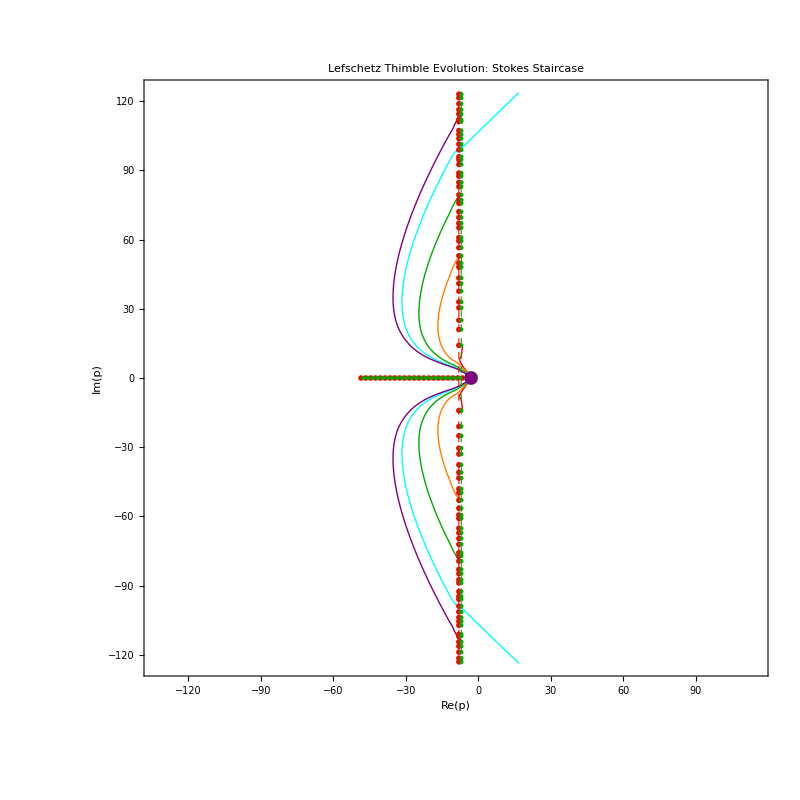

Exported MultiThimbleOverlay.png

Exported ThimbleAnimation.mp4

```mathematica
(* ============================================================ *)
(* Multi-Thimble Overlay: several thimbles on fixed background  *)
(* ============================================================ *)

(* Select representative thimbles at key stages *)
(* Find indices corresponding to specific trapped counts *)
multiIndices = {};
Do[
  Module[{idx = FirstPosition[nTrappedList, n]},
    If[idx =!= Missing["NotFound"],
      AppendTo[multiIndices, idx[[1]]]]
  ],
  {n, {0, 2, 5, 10, 20, 28, 29, 35, 40, 50, 64}}
];

(* Colors for each thimble *)
thimbleColors = {Red, Orange, Darker[Green], Cyan, Purple, Magenta, Brown};

(* Compute all thimble curves *)
thimbleCurves = Table[
  Module[{k = multiIndices[[i]], p0, pFunc, fullPts, re, im},
    p0 = p0Values[[k]];
    pFunc = thimbleData[[k]];
    fullPts = FullThimblePoints[p0, pFunc];
    {Re[fullPts], Im[fullPts]}
  ],
  {i, Length[multiIndices]}
];

(* Determine global bounding box *)
allRe = Flatten[thimbleCurves[[All, 1]]];
allIm = Flatten[thimbleCurves[[All, 2]]];
{xmin, xmax} = MinMax[allRe] + {-0.5, 0.5};
{ymin, ymax} = MinMax[allIm] + {-0.5, 0.5};

(* Make square *)
halfRange = Max[(xmax - xmin)/2, (ymax - ymin)/2];
xCenter = (xmin + xmax)/2;
yCenter = 0;  (* symmetric about real axis *)
xmin = xCenter - halfRange; xmax = xCenter + halfRange;
ymin = -halfRange; ymax = halfRange;

(* Filter visible poles and zeros *)
visPoles = Select[PolePts, 
  xmin <= #[[1]] <= xmax && ymin <= #[[2]] <= ymax &];
visZeros = Select[ZeroPts, 
  xmin <= #[[1]] <= xmax && ymin <= #[[2]] <= ymax &];

(* Build the plot *)
thimblePlotLines = Table[
  Module[{re = thimbleCurves[[i, 1]], im = thimbleCurves[[i, 2]],
           k = multiIndices[[i]], p0, xi, nTr},
    p0 = p0Values[[k]];
    xi = -S1[p0];
    nTr = nTrappedList[[k]];
    Tooltip[
      ListLinePlot[Transpose[{re, im}],
        PlotStyle -> {Thick, thimbleColors[[i]]},
        PlotRange -> All
      ],
      Row[{"ξ=", NumberForm[N[xi], {4, 2}], " trapped=", nTr}]
    ]
  ],
  {i, Length[multiIndices]}
];

(* Legend labels *)
legendLabels = Table[
  Module[{k = multiIndices[[i]], p0, xi, nTr},
    p0 = p0Values[[k]];
    xi = -S1[p0];
    nTr = nTrappedList[[k]];
    Row[{"ξ=", NumberForm[N[xi], {4, 2}], ", N=", nTr}]
  ],
  {i, Length[multiIndices]}
];

(* Combine everything *)
multiThimblePlot = Show[
  (* Thimble curves *)
  Table[
    ListLinePlot[Transpose[{thimbleCurves[[i, 1]], thimbleCurves[[i, 2]]}],
      PlotStyle -> {Thick, thimbleColors[[i]]}],
    {i, Length[multiIndices]}
  ],
  
  (* Poles, zeros, reference lines *)
  Graphics[{
    (* Poles: red dots *)
    Red, PointSize[0.005], Point /@ visPoles,
    (* Zeros: green dots *)
    Darker[Green], PointSize[0.004], Point /@ visZeros,
    (* Saddle points: small colored dots *)
    Table[
      {thimbleColors[[i]], PointSize[0.012], 
       Point[{Re[p0Values[[multiIndices[[i]]]]], 0}]},
      {i, Length[multiIndices]}
    ],
    (* Reference lines *)
    {Dashed, Red, Thickness[0.001], Line[{{-8, ymin}, {-8, ymax}}]},
    {Dashed, Darker[Green], Thickness[0.001], Line[{{-7, ymin}, {-7, ymax}}]}
  }],
  
  Frame -> True,
  FrameLabel -> {"Re(p)", "Im(p)"},
  PlotRange -> {{xmin, xmax}, {ymin, ymax}},
  AspectRatio -> 1,
  ImageSize -> 800,
  Background -> White,
  PlotLabel -> Style["Lefschetz Thimble Evolution: Stokes Staircase", 14, Bold],
  PlotLegends -> Placed[
    LineLegend[thimbleColors[[;; Length[multiIndices]]], legendLabels,
      LegendMarkerSize -> 20],
    {Right, Top}
  ]
];

Print[multiThimblePlot];

(* Export *)
Export[
  FileNameJoin[{NotebookDirectory[], "MultiThimbleOverlay.png"}],
  multiThimblePlot, ImageResolution -> 300
];
Print["Exported MultiThimbleOverlay.png"];

(* === Also export the MP4 animation === *)
Export[
  FileNameJoin[{NotebookDirectory[], "ThimbleAnimation.mp4"}],
  thimblePlots,
  "FrameRate" -> 5,
  ImageResolution -> 150
];
Print["Exported ThimbleAnimation.mp4"];
```

```mathematica
ClearAll[CountTrappedPoles];CountTrappedPoles[pFunc_,zZeros_,xWall_:-8.0`50]:=Module[{vals,reVals,imVals,trapped={},crossings,tn,w1,w2,reCross},If[Head[pFunc]=!=InterpolatingFunction,Return[{}]];vals=pFunc["ValuesOnGrid"];reVals=Re[vals];imVals=Im[vals];Do[tn=zZeros[[n]];crossings=0;Do[If[(imVals[[k]]<=tn&&imVals[[k+1]]>tn)||(imVals[[k]]>=tn&&imVals[[k+1]]<tn),w1=Abs[imVals[[k+1]]-tn];w2=Abs[imVals[[k]]-tn];If[w1+w2>0,reCross=(w1 reVals[[k]]+w2 reVals[[k+1]])/(w1+w2);If[reCross<xWall,crossings++]]],{k,1,Length[vals]-1}];If[OddQ[crossings],AppendTo[trapped,n]],{n,1,Length[zZeros]}];trapped];
```

```mathematica
nRiemann=200;nDyadic=80;RiemannPoles=Table[-8+I Im[N[ZetaZero[n],50]],{n,nRiemann}];Poles=RiemannPoles;zZeros=Im/@RiemannPoles;DyadicPoles=Table[-17/2+I 2 Pi k/Log[2],{k,1,nDyadic}];zDyadic=Im/@DyadicPoles;Print["Riemann poles = ",Length[RiemannPoles],"  dyadic positive poles = ",Length[DyadicPoles],"  first dyadic Im = ",N[zDyadic[[1]]]];
```

Riemann poles = 200  dyadic positive poles = 80  first dyadic Im = 9.06472

```mathematica
trapData=Table[Module[{pFunc=thimbleData[[k]],r,d},If[Head[pFunc]=!=InterpolatingFunction,{-1,-1,-1,{},{}},r=CountTrappedPoles[pFunc,zZeros,-8.0`50];d=CountTrappedPoles[pFunc,zDyadic,-17/2];{Length[r],Length[d],Length[r]+Length[d],r,d}]],{k,Length[thimbleData]}];nTrappedRiemannList=trapData[[All,1]];nTrappedDyadicList=trapData[[All,2]];nTrappedList=trapData[[All,3]];trappedRiemannIdxList=trapData[[All,4]];trappedDyadicIdxList=trapData[[All,5]];staircasePoints=Table[{N[-S1Interp[p0Values[[k]]]],nTrappedList[[k]]},{k,Length[p0Values]}];Print["max Riemann = ",Max[nTrappedRiemannList],"  max dyadic = ",Max[nTrappedDyadicList],"  max total = ",Max[nTrappedList]];
```

max Riemann = 62  max dyadic = 18  max total = 80

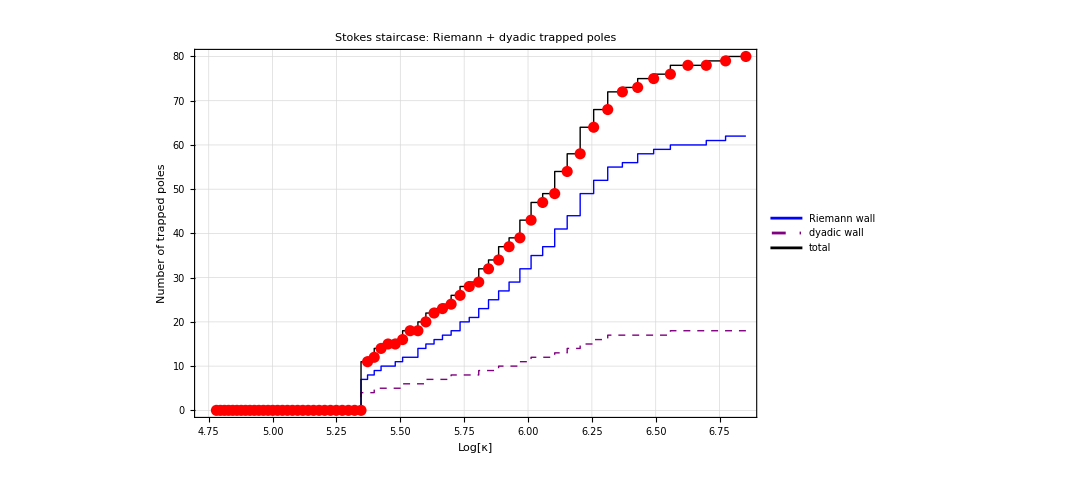

```mathematica
stairR=Table[{N[-S1Interp[p0Values[[k]]]],nTrappedRiemannList[[k]]},{k,Length[p0Values]}];stairD=Table[{N[-S1Interp[p0Values[[k]]]],nTrappedDyadicList[[k]]},{k,Length[p0Values]}];stairT=Table[{N[-S1Interp[p0Values[[k]]]],nTrappedList[[k]]},{k,Length[p0Values]}];ListStepPlot[{stairR,stairD,stairT},Frame->True,FrameLabel->{"Log[κ]","Number of trapped poles"},PlotLabel->"Stokes staircase: Riemann + dyadic trapped poles",PlotLegends->{"Riemann wall","dyadic wall","total"},PlotStyle->{{Thick,Blue},{Thick,Purple,Dashed},{Thick,Black}},PlotRange->All,GridLines->Automatic,ImageSize->800,Epilog->{Red,PointSize[0.01],Point[stairT]}]
```

```mathematica
DyadicPolePts=Join[Table[{N[-17/2],N[2 Pi k/Log[2]]},{k,1,nDyadic}],Table[{N[-17/2],N[-2 Pi k/Log[2]]},{k,1,nDyadic}]];PolePts=DeleteDuplicates[Join[PolePts,DyadicPolePts]];Print["PolePts including dyadic wall = ",Length[PolePts]];
```

PolePts including dyadic wall = 583

```mathematica
DyadicPolePts=Join[Table[{N[-17/2],N[2 Pi k/Log[2]]},{k,1,nDyadic}],Table[{N[-17/2],N[-2 Pi k/Log[2]]},{k,1,nDyadic}]];PolePts=DeleteDuplicates[Join[PolePts,DyadicPolePts]];Print["PolePts including dyadic wall = ",Length[PolePts]];
```

PolePts including dyadic wall = 583

Found 5 thimbles for overlay

Trapped counts: {0,20,28,29,64}

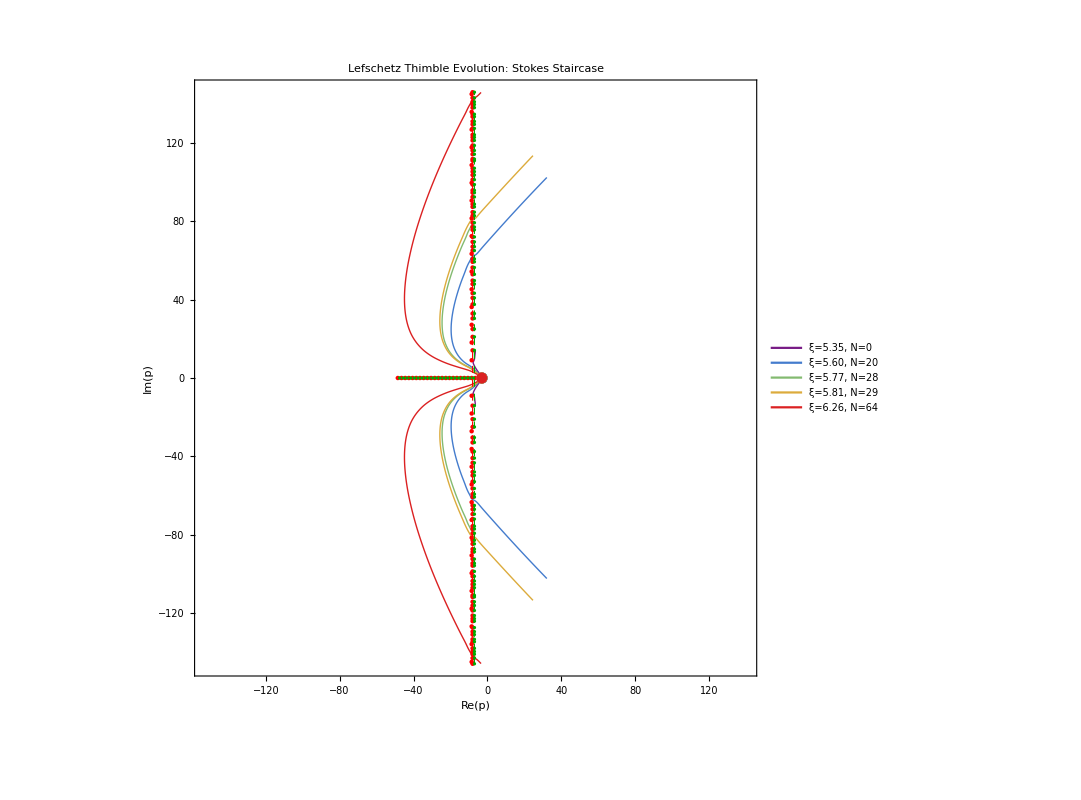

Exported MultiThimbleOverlay.png

```mathematica
(* ============================================================ *)
(* Multi-Thimble Overlay: FIXED colors and legend               *)
(* ============================================================ *)

(* Select representative thimbles at key stages *)
multiIndices = {};
Do[
  Module[{idx = FirstPosition[nTrappedList, n]},
    If[idx =!= Missing["NotFound"],
      AppendTo[multiIndices, idx[[1]]]]
  ],
  {n, {0, 2, 5, 10, 20, 28, 29, 35, 40, 50, 64}}
];

Print["Found ", Length[multiIndices], " thimbles for overlay"];
Print["Trapped counts: ", nTrappedList[[#]] & /@ multiIndices];

(* Generate enough distinct colors for ALL found indices *)
thimbleColors = ColorData["Rainbow"] /@ Subdivide[0, 1, Max[Length[multiIndices] - 1, 1]];

(* Compute all thimble curves *)
thimbleCurves = Table[
  Module[{k = multiIndices[[i]], p0, pFunc, fullPts},
    p0 = p0Values[[k]];
    pFunc = thimbleData[[k]];
    fullPts = FullThimblePoints[p0, pFunc];
    {Re[fullPts], Im[fullPts]}
  ],
  {i, Length[multiIndices]}
];

(* Determine global bounding box *)
allRe = Flatten[thimbleCurves[[All, 1]]];
allIm = Flatten[thimbleCurves[[All, 2]]];
{xmin, xmax} = MinMax[allRe] + {-0.5, 0.5};
{ymin, ymax} = MinMax[allIm] + {-0.5, 0.5};

(* Make square *)
halfRange = Max[(xmax - xmin)/2, (ymax - ymin)/2];
xCenter = (xmin + xmax)/2;
xmin = xCenter - halfRange; xmax = xCenter + halfRange;
ymin = -halfRange; ymax = halfRange;

(* Filter visible poles and zeros *)
visPoles = Select[PolePts, 
  xmin <= #[[1]] <= xmax && ymin <= #[[2]] <= ymax &];
visZeros = Select[ZeroPts, 
  xmin <= #[[1]] <= xmax && ymin <= #[[2]] <= ymax &];

(* Legend labels *)
legendLabels = Table[
  Module[{k = multiIndices[[i]], p0, xi, nTr},
    p0 = p0Values[[k]];
    xi = -S1[p0];
    nTr = nTrappedList[[k]];
    StringForm["ξ=``, N=``", NumberForm[N[xi], {4, 2}], nTr]
  ],
  {i, Length[multiIndices]}
];

(* Combine everything *)
multiThimblePlot = Show[
  (* Thimble curves — one per found index *)
  Table[
    ListLinePlot[
      Transpose[{thimbleCurves[[i, 1]], thimbleCurves[[i, 2]]}],
      PlotStyle -> {Thick, thimbleColors[[i]]}
    ],
    {i, Length[multiIndices]}
  ],
  
  (* Poles, zeros, reference lines *)
  Graphics[{
    (* Poles: red dots *)
    Red, PointSize[0.004], Point /@ visPoles,
    (* Zeros: green dots *)
    Darker[Green], PointSize[0.003], Point /@ visZeros,
    (* Saddle points: colored dots on real axis *)
    Table[
      {thimbleColors[[i]], PointSize[0.010], 
       Point[{N[Re[p0Values[[multiIndices[[i]]]]]], 0}]},
      {i, Length[multiIndices]}
    ],
    (* Reference lines *)
    {Dashed, Red, Thickness[0.001], Line[{{-8, ymin}, {-8, ymax}}]},
    {Dashed, Darker[Green], Thickness[0.001], Line[{{-7, ymin}, {-7, ymax}}]}
  }],
  
  Frame -> True,
  FrameLabel -> {"Re(p)", "Im(p)"},
  PlotRange -> {{xmin, xmax}, {ymin, ymax}},
  AspectRatio -> 1,
  ImageSize -> 800,
  Background -> White,
  PlotLabel -> Style["Lefschetz Thimble Evolution: Stokes Staircase", 14, Bold]
];

(* Add legend separately using Legended *)
multiThimblePlotWithLegend = Legended[multiThimblePlot,
  Placed[
    LineLegend[thimbleColors[[;; Length[multiIndices]]], legendLabels,
      LegendMarkerSize -> 20, LegendFunction -> "Frame"],
    {Right, Top}
  ]
];

Print[multiThimblePlotWithLegend];

(* Export *)
Export[
  FileNameJoin[{NotebookDirectory[], "MultiThimbleOverlay.png"}],
  multiThimblePlotWithLegend, ImageResolution -> 300
];
Print["Exported MultiThimbleOverlay.png"];
```

Selected indices: {35,45,54,26}

Trapped counts: {0,0,0,20}

xi values: {5.34619,5.11833,4.94615,5.60006}

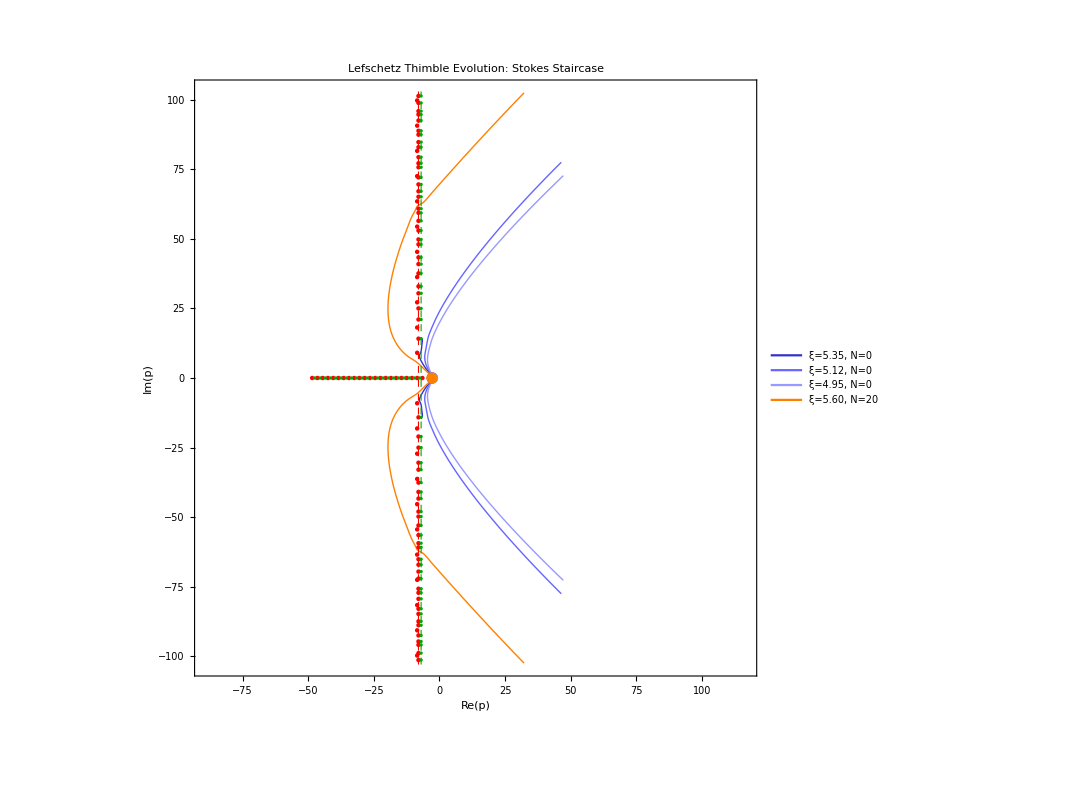

Exported MultiThimbleOverlay.png

```mathematica
(* ============================================================ *)
(* Multi-Thimble Overlay: 3 WITHOUT trapped poles + 3 WITH      *)
(* Show the transition clearly                                  *)
(* ============================================================ *)

(* Find indices for thimbles WITHOUT trapped poles (N=0) at different xi *)
zeroIndices = Flatten[Position[nTrappedList, 0]];
(* Pick 3 evenly spaced from the N=0 range *)
noTrapIndices = zeroIndices[[Round[Subdivide[1, Length[zeroIndices], 3]][[{1, 2, 3}]]]];

(* Find indices for thimbles WITH trapped poles: pick N=1, 5, 20 *)
withTrapIndices = {};
Do[
  Module[{idx = FirstPosition[nTrappedList, n]},
    If[idx =!= Missing["NotFound"],
      AppendTo[withTrapIndices, idx[[1]]]]
  ],
  {n, {1, 5, 20}}
];

multiIndices = Join[noTrapIndices, withTrapIndices];

Print["Selected indices: ", multiIndices];
Print["Trapped counts: ", nTrappedList[[#]] & /@ multiIndices];
Print["xi values: ", N[-S1[p0Values[[#]]]] & /@ multiIndices];

(* Generate enough distinct colors *)
(* Blue shades for N=0, warm colors for N>0 *)
thimbleColors = {
  RGBColor[0.2, 0.2, 0.8],    (* dark blue: N=0, early *)
  RGBColor[0.4, 0.4, 1.0],    (* medium blue: N=0, middle *)
  RGBColor[0.6, 0.6, 1.0],    (* light blue: N=0, late *)
  RGBColor[1.0, 0.5, 0.0],    (* orange: N=1 *)
  RGBColor[0.8, 0.0, 0.0],    (* red: N=5 *)
  RGBColor[0.5, 0.0, 0.5]     (* purple: N=20 *)
};

(* Compute all thimble curves *)
thimbleCurves = Table[
  Module[{k = multiIndices[[i]], p0, pFunc, fullPts},
    p0 = p0Values[[k]];
    pFunc = thimbleData[[k]];
    fullPts = FullThimblePoints[p0, pFunc];
    {Re[fullPts], Im[fullPts]}
  ],
  {i, Length[multiIndices]}
];

(* Determine global bounding box *)
allRe = Flatten[thimbleCurves[[All, 1]]];
allIm = Flatten[thimbleCurves[[All, 2]]];
{xmin, xmax} = MinMax[allRe] + {-0.5, 0.5};
{ymin, ymax} = MinMax[allIm] + {-0.5, 0.5};

(* Make square *)
halfRange = Max[(xmax - xmin)/2, (ymax - ymin)/2];
xCenter = (xmin + xmax)/2;
xmin = xCenter - halfRange; xmax = xCenter + halfRange;
ymin = -halfRange; ymax = halfRange;

(* Filter visible poles and zeros *)
visPoles = Select[PolePts, 
  xmin <= #[[1]] <= xmax && ymin <= #[[2]] <= ymax &];
visZeros = Select[ZeroPts, 
  xmin <= #[[1]] <= xmax && ymin <= #[[2]] <= ymax &];

(* Legend labels *)
legendLabels = Table[
  Module[{k = multiIndices[[i]], xi, nTr},
    xi = N[-S1[p0Values[[k]]]];
    nTr = nTrappedList[[k]];
    Style[Row[{"ξ=", NumberForm[xi, {4, 2}], ", N=", nTr}], 12]
  ],
  {i, Length[multiIndices]}
];

(* Combine everything *)
multiThimblePlot = Show[
  (* Thimble curves *)
  Table[
    ListLinePlot[
      Transpose[{thimbleCurves[[i, 1]], thimbleCurves[[i, 2]]}],
      PlotStyle -> {Thick, thimbleColors[[i]]}
    ],
    {i, Length[multiIndices]}
  ],
  
  (* Poles, zeros, reference lines *)
  Graphics[{
    (* Poles: red dots *)
    Red, PointSize[0.004], Point /@ visPoles,
    (* Zeros: green dots *)
    Darker[Green], PointSize[0.003], Point /@ visZeros,
    (* Saddle points: colored dots on real axis *)
    Table[
      {thimbleColors[[i]], PointSize[0.010], 
       Point[{N[Re[p0Values[[multiIndices[[i]]]]]], 0}]},
      {i, Length[multiIndices]}
    ],
    (* Reference lines *)
    {Dashed, Red, Thickness[0.001], Line[{{-8, ymin}, {-8, ymax}}]},
    {Dashed, Darker[Green], Thickness[0.001], Line[{{-7, ymin}, {-7, ymax}}]}
  }],
  
  Frame -> True,
  FrameLabel -> {"Re(p)", "Im(p)"},
  PlotRange -> {{xmin, xmax}, {ymin, ymax}},
  AspectRatio -> 1,
  ImageSize -> 800,
  Background -> White,
  PlotLabel -> Style["Lefschetz Thimble Evolution: Stokes Staircase", 14, Bold]
];

(* Add legend using Legended *)
multiThimblePlotWithLegend = Legended[multiThimblePlot,
  Placed[
    LineLegend[thimbleColors[[;; Length[multiIndices]]], legendLabels,
      LegendMarkerSize -> 25, LegendFunction -> "Frame"],
    {Right, Top}
  ]
];

Print[multiThimblePlotWithLegend];

(* Export *)
Export[
  FileNameJoin[{NotebookDirectory[], "MultiThimbleOverlay.png"}],
  multiThimblePlotWithLegend, ImageResolution -> 300
];
Print["Exported MultiThimbleOverlay.png"];
```

```mathematica
ClearAll[CalculateRiemannResidue,CalculateDyadicResidue,ADouble,ALogDer,CalculateCentralDyadicDoubleResidue];CalculateRiemannResidue[pVal_,xi_]:=Module[{p=pVal},Exp[xi p] DF[p,0] Gamma[-p] Zeta[p+15/2]/((2 p+7)(2 p+17) Zeta'[p+17/2](1-2^(-(p+17/2))))];CalculateDyadicResidue[pVal_,xi_]:=Module[{p=pVal},Exp[xi p] DF[p,0] Gamma[-p] Zeta[p+15/2]/((2 p+7)(2 p+17) Zeta[p+17/2] Log[2])];ADouble[p_?NumericQ,xi_?NumericQ]:=Exp[xi p] DF[p,0] Gamma[-p] Zeta[p+15/2]/((2 p+7) Zeta[p+17/2]);ALogDer[p_?NumericQ,xi_?NumericQ]:=xi+DF[p,1]/DF[p,0]-PolyGamma[0,-p]+Zeta'[p+15/2]/Zeta[p+15/2]-2/(2 p+7)-Zeta'[p+17/2]/Zeta[p+17/2];CalculateCentralDyadicDoubleResidue[xi_?NumericQ]:=Module[{p=-17/2,A0,A1},A0=ADouble[p,xi];A1=A0 ALogDer[p,xi];A1/(2 Log[2])+A0/4];
```

```mathematica
Print["Computing H(xi) with Riemann + dyadic residues..."];results=ParallelTable[Module[{p0,pFunc,xi,rIdx,dIdx,ghSum,S0,thimbleContrib,rSum,dSum,residueContrib},p0=p0Values[[k]];pFunc=thimbleData[[k]];xi=-S1[p0];If[Head[pFunc]=!=InterpolatingFunction,{N[xi],0.,0.,0.,0.,0.},S0=S[p0]+xi p0;ghSum=ThimbleGHSum[p0,pFunc,xi];thimbleContrib=(1/Pi) Im[Exp[S0] ghSum];rIdx=CountTrappedPoles[pFunc,zZeros,-8.0`50];dIdx=CountTrappedPoles[pFunc,zDyadic,-17/2];rSum=If[Length[rIdx]>0,Total[CalculateRiemannResidue[RiemannPoles[[#]],xi]&/@rIdx],0+0 I];dSum=If[Length[dIdx]>0,Total[CalculateDyadicResidue[DyadicPoles[[#]],xi]&/@dIdx],0+0 I];residueContrib=2 Re[rSum+dSum];{N[xi],thimbleContrib+residueContrib,residueContrib,thimbleContrib,2 Re[rSum],2 Re[dSum]}]],{k,Length[thimbleData]}];Print["Done. ",Length[results]," points computed."];
```

Computing H(xi) with Riemann + dyadic residues...

Done. 64 points computed.

```mathematica
xiVals=results[[All,1]];hTotal=results[[All,2]];hRes=results[[All,3]];hThimb=results[[All,4]];hResR=results[[All,5]];hResD=results[[All,6]];Print["H_total range = ",MinMax[hTotal]];Print["H_Riemann residue range = ",MinMax[hResR]];Print["H_dyadic residue range = ",MinMax[hResD]];Print["H_thimble range = ",MinMax[hThimb]];ListLinePlot[{Transpose[{xiVals,hTotal}],Transpose[{xiVals,hResR}],Transpose[{xiVals,hResD}],Transpose[{xiVals,hThimb}]},PlotStyle->{{Thick,Black},{Thick,Blue,Dashed},{Thick,Purple,Dashed},{Thick,Red,Dashed}},Frame->True,FrameLabel->{"ξ","H(ξ)"},PlotLabel->"Odd spectrum: total, Riemann residues, dyadic residues, thimble",PlotLegends->{"total","Riemann residues","dyadic residues","thimble"},PlotRange->All,GridLines->Automatic,ImageSize->800]
```

H_total range = {6.92195×10^-7,0.000799068}

H_Riemann residue range = {-4.09742×10^-12,6.88698×10^-13}

H_dyadic residue range = {-1.15409×10^-10,2.191×10^-9}

H_thimble range = {6.92195×10^-7,0.000799068}

```mathematica
resultsOddDyadic=results;xiValsOddDyadic=xiVals;hTotalOddDyadic=hTotal;hResOddDyadic=hRes;hThimbOddDyadic=hThimb;hResROddDyadic=hResR;hResDOddDyadic=hResD;theordataOddDyadic=SortBy[Chop[N[Transpose[{xiValsOddDyadic,hTotalOddDyadic}]]],First];Print["Saved odd+dyadic theory: ",Length[theordataOddDyadic]," points, H range = ",MinMax[theordataOddDyadic[[All,2]]]];
```

Saved odd+dyadic theory: 64 points, H range = {6.92195×10^-7,0.000799068}

```mathematica
theordata=theordataOddDyadic;
```

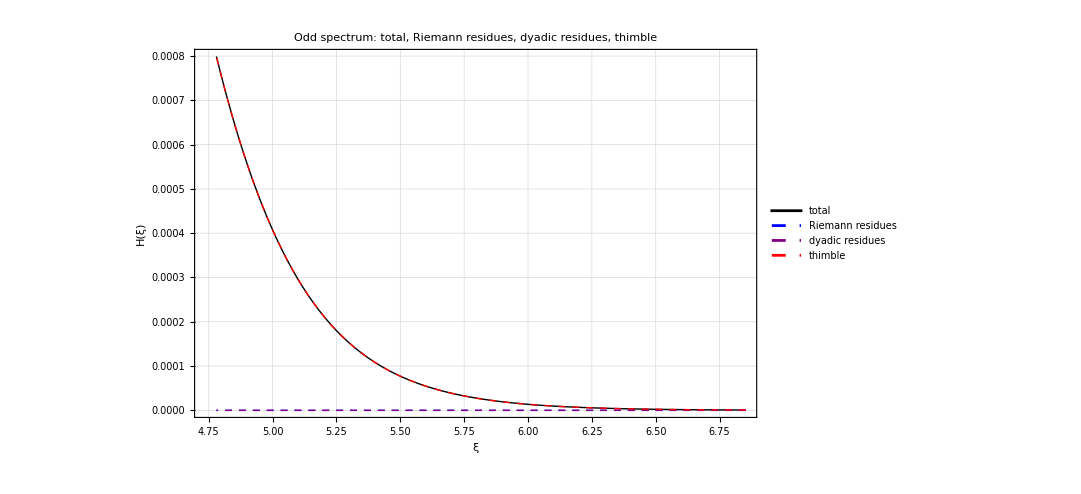

```mathematica
ListLinePlot[{Transpose[{xiValsOddDyadic,hTotalOddDyadic}],Transpose[{xiValsOddDyadic,hResROddDyadic}],Transpose[{xiValsOddDyadic,hResDOddDyadic}],Transpose[{xiValsOddDyadic,hThimbOddDyadic}]},PlotStyle->{{Thick,Black},{Thick,Blue,Dashed},{Thick,Purple,Dashed},{Thick,Red,Dashed}},Frame->True,FrameLabel->{"ξ","H(ξ)"},PlotLabel->"Odd spectrum: total, Riemann residues, dyadic residues, thimble",PlotLegends->{"total","Riemann residues","dyadic residues","thimble"},PlotRange->All,GridLines->Automatic,ImageSize->800]
```

```mathematica
DyadicPoles=Table[-17/2+I 2 Pi k/Log[2],{k,1,nDyadic}];
```

```mathematica
(* ==========================================================*)
(*RECOVERED DNS  ALGORITHM*)(* ==========================================================*)
SpectrumFromDNS[N0_, N1_]:=Block[{dnsInterp,kMin,kMax,OLambda,filteredPoints,rawDNSData,sdatas},
rawDNSData=ToExpression /@Import[NotebookDirectory[]<>"/July25_4Kdata/4096cube_ek.txt","Table"];
sdatas=rawDNSData[[N0;;N1]];
(*1. Create a smooth interpolation of the raw DNS Energy Spectrum*)
(* ==========================================================*)(*OPTIMIZED VECTORIZED& PARALLELIZED PHASE-LOCKED H(kappa)*)(* ==========================================================*)Quiet@LaunchKernels[];
(*Use MachinePrecision floats (N) for blazing fast C-level vector math*)
numSnaps=Length[sdatas];
      kMaxGrid=Length[sdatas[[1]]];

(*Safe upper limit*)
kMaxEval=Floor[kMaxGrid];

(*Pre-compute static numerical arrays before the loops even start*)
kSumRange=N[Range[2,kMaxEval]];
	logKSumRange=Log[kSumRange];
	kSumRangeSq=kSumRange^2;

DistributeDefinitions[λOptN,c1,kSumRange,logKSumRange,kSumRangeSq,sdatas];

PrintTemporary["Processing ",numSnaps," snapshots on ",$KernelCount," parallel cores..."];

(*PARALLEL OUTER LOOP:ParallelTable builds local matrices across CPU cores and Flatten merges them instantly.*)
allScatteredData=Flatten[ParallelTable[Block[{Einterp,FEv,weights,sumFEk2,sumFEk2Logk,meanLogK,Ln,kappaNArray,HArray},Einterp=Interpolation[sdatas[[n]],InterpolationOrder->3,Method->"Spline"];
(*1) VECTORIZED FE EVALUATION*)(*InterpolatingFunction natively threads over lists in modern Mathematica!*)
FEv=Einterp[kSumRange];
(*2) VECTORIZED MOMENTS via listable array arithmetic and Total*)
weights=FEv*kSumRangeSq;
sumFEk2=Total[weights];
If[sumFEk2!=0,sumFEk2Logk=Total[weights*logKSumRange];
meanLogK=sumFEk2Logk/sumFEk2;
Ln=Exp[-meanLogK];
(*3) VECTORIZED H and Kappa calculation*)kappaNArray=kSumRange*Ln;
HArray=(FEv)/sumFEk2;
(*4) Instant Transpose instead of AppendTo loop*)(*This instantly creates the Nx2 matrix:{{Log[k1],H1},{Log[k2],H2},...}*)Transpose[{Log[kappaNArray],HArray}],{} (*Return empty if sum is exactly 0*)]],{n,1,numSnaps}],1 (*Flattens the array of snapshot matrices into a single list of {x,y} pairs*)];

Print["Extracted ",Length[allScatteredData]," phase-locked points. Binning..."];

(* ==========================================================*)(*FAST LOGARITHMIC BINNING AND ERROR CALCULATION*)(* ==========================================================*)binWidth=0.02;

binnedData=GatherBy[allScatteredData,Round[#[[1]],binWidth]&];

finalTable=Flatten[Table[Block[{lnKappaVals=bin[[All,1]],HVals=bin[[All,2]]},If[Length[HVals]>5,(*Require enough points for valid statistics*){{Mean[lnKappaVals],Mean[HVals],StandardDeviation[HVals]/Sqrt[Length[HVals]]}},{}]],{bin,binnedData}],1];

finalTable=SortBy[finalTable,First];

(* ==========================================================*)
(*RENDER RED PLOT WITH NATIVE ERROR BARS*)
(* ==========================================================*)
plotDataAround={#[[1]],Around[#[[2]],#[[3]]]}&/@finalTable;

Print[ListPlot[plotDataAround,PlotRange->All,PlotStyle->{Red},PlotLegends->{"DNS"}]];
plotDataAround
];
```

Extracted 2253747 phase-locked points. Binning...

General::munfl: 6.32423×10^-155 6.32423×10^-155 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.88881×10^-161 9.88881×10^-161 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.3263×10^-166 2.3263×10^-166 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

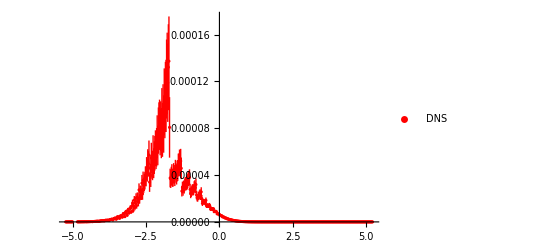

```mathematica
dnsTab = SpectrumFromDNS[100, 1200];
```

```mathematica
rangedata =Select[dnsTab, #[[1]]>-0.2&& #[[2]]> 3*10^-7&];
```

General::munfl: 6.17993×10^-159 6.17993×10^-159 is too small to represent as a normalized machine number; precision may be lost.

```mathematica
rangedata[[;;10]]
```

{{-0.2,0.000011114},{-0.179989,8.71.010^-6},{-0.159984,9.21.110^-6},{-0.139956,8.81.110^-6},{-0.119933,9.01.110^-6},{-0.0999471,8.61.010^-6},{-0.0799436,6.90.810^-6},{-0.0599722,6.90.810^-6},{-0.0399614,6.80.710^-6},{-0.0199163,6.80.810^-6}}

```mathematica
ClearAll[a,b,c,x];
```

```mathematica
nlm=NonlinearModelFit[rangedata,{ a E^(-3.5 x)  +b E^(-6.5 x) + c E^(-8.5 x) },{a,b,c},x];
```

```mathematica
nlm[x]
```

-4.03436×10^-6 ⅇ^(-8.5 x)+5.46774×10^-6 ⅇ^(-6.5 x)+5.19705×10^-6 ⅇ^(-3.5 x)

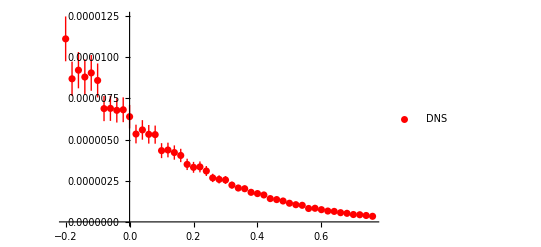

```mathematica
pdns=ListPlot[rangedata,PlotStyle->{Red},PlotLegends->{ "DNS"}]
```

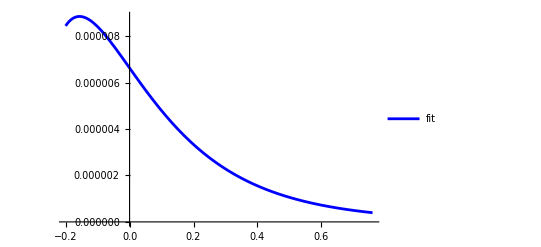

```mathematica
ptheor =  Plot[nlm[ξ], {ξ, rangedata[[1,1]],rangedata[[-1,1]]},PlotStyle->{Blue},PlotLegends->{ "fit"}]
```

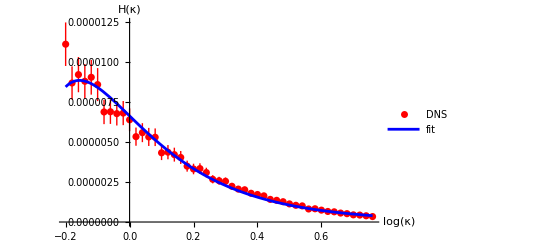

```mathematica
Show[{pdns,ptheor},AxesLabel->{Log[κ], H[κ]}]
```

```mathematica
theordata=Transpose[{xiVals, hTotal}]
```

{{6.85298,6.92195×10^-7},{6.77346,9.14263×10^-7},{6.69787,1.191×10^-6},{6.62592,1.53185×10^-6},{6.55734,1.94713×10^-6},{6.49187,2.44806×10^-6},{6.4293,3.04676×10^-6},{6.36942,3.75621×10^-6},{6.31204,4.59024×10^-6},{6.257,5.5635×10^-6},{6.20415,6.69142×10^-6},{6.15334,7.99022×10^-6},{6.10445,9.47682×10^-6},{6.05736,0.0000111689},{6.01196,0.0000130847},{5.96814,0.000015243},{5.92583,0.0000176634},{5.88492,0.0000203657},{5.84535,0.0000233703},{5.80703,0.000026698},{5.76991,0.0000303704},{5.73391,0.0000344085},{5.69898,0.0000388344},{5.66506,0.0000436699},{5.6321,0.0000489375},{5.60006,0.0000546593},{5.56889,0.0000608575},{5.53854,0.0000675552},{5.50897,0.0000747734},{5.48016,0.0000825349},{5.45206,0.0000908627},{5.42465,0.0000997769},{5.39788,0.0001093},{5.37174,0.000119454},{5.34619,0.000130256},{5.32121,0.000141727},{5.29677,0.000153891},{5.27285,0.000166765},{5.24944,0.000180368},{5.2265,0.000194717},{5.20402,0.00020983},{5.18198,0.000225726},{5.16036,0.000242418},{5.13915,0.000259924},{5.11833,0.000278257},{5.09788,0.000297434},{5.07779,0.000317466},{5.05804,0.000338367},{5.03863,0.00036015},{5.01954,0.000382824},{5.00076,0.000406404},{4.98227,0.000430897},{4.96407,0.000456315},{4.94615,0.000482665},{4.92849,0.000509956},{4.91108,0.000538196},{4.89393,0.000567393},{4.87701,0.000597553},{4.86032,0.000628683},{4.84385,0.00066079},{4.82759,0.000693876},{4.81154,0.00072795},{4.79569,0.000763009},{4.78003,0.000799068}}

```mathematica
rangedata
```

{{-0.2,0.000011114},{-0.179989,8.71.010^-6},{-0.159984,9.21.110^-6},{-0.139956,8.81.110^-6},{-0.119933,9.01.110^-6},{-0.0999471,8.61.010^-6},{-0.0799436,6.90.810^-6},{-0.0599722,6.90.810^-6},{-0.0399614,6.80.710^-6},{-0.0199163,6.80.810^-6},{0.0000375013,6.40.710^-6},{0.0200299,5.30.610^-6},{0.0400251,5.60.610^-6},{0.0599908,5.30.610^-6},{0.0800289,5.30.610^-6},{0.100025,4.30.510^-6},{0.120005,4.40.410^-6},{0.139996,4.20.410^-6},{0.160005,4.00.410^-6},{0.180034,3.490.3410^-6},{0.200023,3.310.3310^-6},{0.220056,3.340.3310^-6},{0.240053,3.090.3010^-6},{0.260004,2.670.2510^-6},{0.280032,2.580.2510^-6},{0.300057,2.550.2410^-6},{0.320076,2.230.2010^-6},{0.340074,2.060.1910^-6},{0.360013,2.010.1810^-6},{0.380004,1.800.1610^-6},{0.400022,1.720.1510^-6},{0.420017,1.640.1510^-6},{0.440027,1.410.1310^-6},{0.460058,1.360.1210^-6},{0.48006,1.270.1110^-6},{0.500054,1.130.1010^-6},{0.520057,1.040.0910^-6},{0.540034,1.010.0810^-6},{0.560015,8.10.710^-7},{0.580024,8.30.710^-7},{0.600036,7.40.610^-7},{0.620046,6.60.510^-7},{0.640033,6.40.510^-7},{0.660013,5.60.410^-7},{0.680012,5.20.410^-7},{0.700009,4.480.3510^-7},{0.720006,4.340.3210^-7},{0.740016,3.900.2910^-7},{0.760038,3.400.2510^-7}}

```mathematica
rangedata[[1,2]]["Error"]
```

1.36074×10^-6

xiShift = 5.05

AScale = 0.0166013

Relative error = 0.00780388

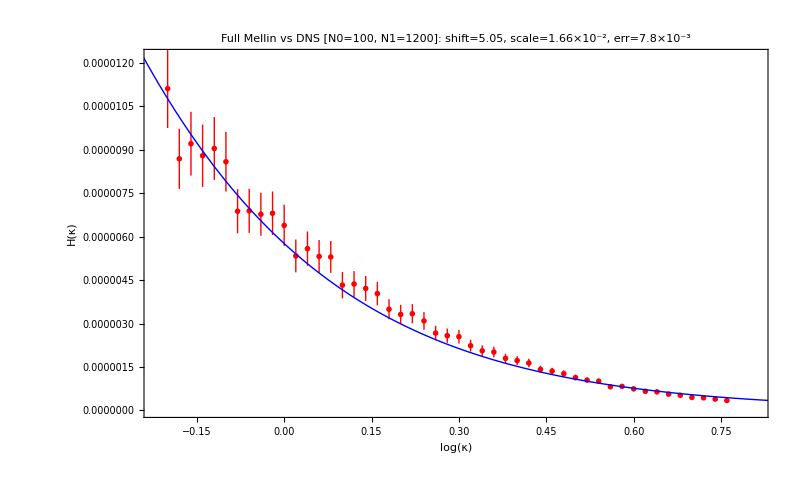

```mathematica
(* ============================================================ *)
(* Fit new rangedata [N0=150, N1=1000] to full Mellin theory    *)
(* ============================================================ *)

(* Theory interpolation *)
theoryInterp = Interpolation[theordata, InterpolationOrder -> 3];
{xiMin, xiMax} = theoryInterp["Domain"][[1]];

(* DNS tail: extract numerical values from rangedata *)
rdX = #[[1]] & /@ rangedata;
rdY = #[[2]]["Value"] & /@ rangedata;
rdE = #[[2]]["Error"]^2 & /@ rangedata;

(* Simple scan for best shift and scale *)
bestErr = Infinity; bestXS = 0; bestA = 1;
Do[
  Module[{overlap, dX, dY, tY, sc, err},
    overlap = Select[Transpose[{rdX, rdY, rdE}], 
      xiMin <= #[[1]] + xs <= xiMax &];
    If[Length[overlap] < 10, Continue[]];
    dX = overlap[[All, 1]];
    dY = overlap[[All, 2]];
    dE = overlap[[All, 3]];
    tY = theoryInterp[# + xs] & /@ dX;
    sc = Total[dY * tY/dE] / Total[tY^2/dE];
    err = Total[(dY - sc * tY)^2] / Total[dY^2];
    If[err < bestErr, bestErr = err; bestXS = xs; bestA = sc];
  ],
  {xs, 4.0, 6.0, 0.005}
];

Print["xiShift = ", bestXS];
Print["AScale = ", bestA];
Print["Relative error = ", bestErr];

(* Theory shifted to DNS frame *)
theoryShifted = Table[
  {xi - bestXS, bestA * theoryInterp[xi]},
  {xi, xiMin, xiMax, 0.005}
];

(* Plot *)
Show[
  ListPlot[rangedata, PlotStyle -> {Red, PointSize[0.005]}, 
    PlotRange -> All, Frame -> True,
    FrameLabel -> {"log(κ)", "H(κ)"},
    ImageSize -> 800],
  ListLinePlot[theoryShifted, PlotStyle -> {Blue, Thick}],
  PlotRange -> {
    {Min[rdX] - 0.02, Max[rdX] + 0.05},
    {0, 1.1 Max[rdY]}
  },
  PlotLabel -> Style[Row[{
    "Full Mellin vs DNS [N0=100, N1=1200]: shift=", NumberForm[bestXS, 4],
    ", scale=", ScientificForm[bestA, 3],
    ", err=", ScientificForm[bestErr, 2]}], 13, Bold]
]
```

Extracted 1741997 phase-locked points. Binning...

General::munfl: (2.21487×10^-305)/8423 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.14891×10^-161 5.14891×10^-161 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.36523×10^-169 6.36523×10^-169 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

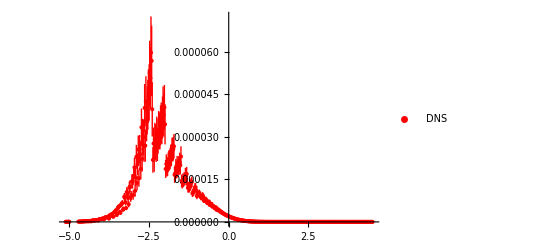

```mathematica
dnsTab1 = SpectrumFromDNS[150, 1000];
```

```mathematica
rangedata1 =Select[dnsTab1, #[[1]]>0.&& #[[2]]> 10^-7&];
```

General::munfl: 5.58703×10^-157 5.58703×10^-157 is too small to represent as a normalized machine number; precision may be lost.

xiShift = 6.

AScale = 0.1491

Relative error = 0.003499

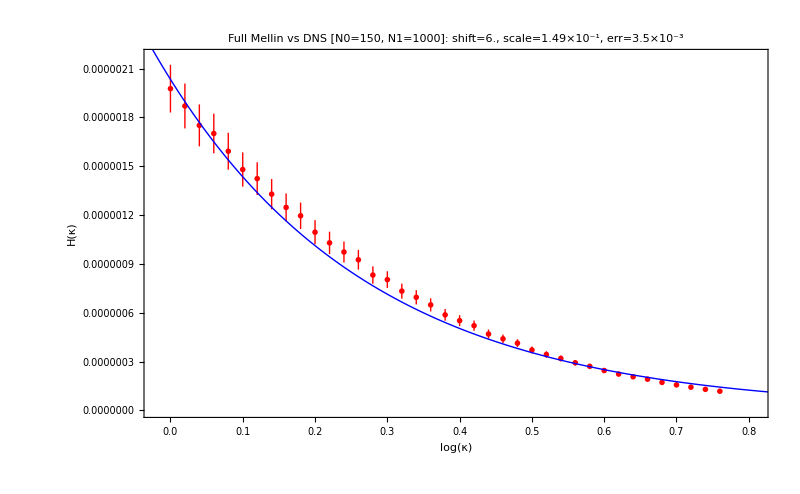

```mathematica
(* ============================================================ *)
(* Fit new rangedata [N0=150, N1=1000] to full Mellin theory    *)
(* ============================================================ *)

(* Theory interpolation *)
theoryInterp = Interpolation[theordata, InterpolationOrder -> 3];
{xiMin, xiMax} = theoryInterp["Domain"][[1]];

(* DNS tail: extract numerical values from rangedata *)
rdX = #[[1]] & /@ rangedata1;
rdY = #[[2]]["Value"] & /@ rangedata1;
rdE = #[[2]]["Error"]^2 & /@ rangedata1;

(* Simple scan for best shift and scale *)
bestErr = Infinity; bestXS = 0; bestA = 1;
Do[
  Module[{overlap, dX, dY, tY, sc, err},
    overlap = Select[Transpose[{rdX, rdY, rdE}], 
      xiMin <= #[[1]] + xs <= xiMax &];
    If[Length[overlap] < 10, Continue[]];
    dX = overlap[[All, 1]];
    dY = overlap[[All, 2]];
    dE = overlap[[All, 3]];
    tY = theoryInterp[# + xs] & /@ dX;
    sc = Total[dY * tY/dE] / Total[tY^2/dE];
    err = Total[(dY - sc * tY)^2] / Total[dY^2];
    If[err < bestErr, bestErr = err; bestXS = xs; bestA = sc];
  ],
  {xs, 4.0, 6.0, 0.005}
];

Print["xiShift = ", bestXS];
Print["AScale = ", bestA];
Print["Relative error = ", bestErr];

(* Theory shifted to DNS frame *)
theoryShifted = Table[
  {xi - bestXS, bestA * theoryInterp[xi]},
  {xi, xiMin, xiMax, 0.005}
];

(* Plot *)
Show[
  ListPlot[rangedata1, PlotStyle -> {Red, PointSize[0.005]}, 
    PlotRange -> All, Frame -> True,
    FrameLabel -> {"log(κ)", "H(κ)"},
    ImageSize -> 800],
  ListLinePlot[theoryShifted, PlotStyle -> {Blue, Thick}],
  PlotRange -> {
    {Min[rdX] - 0.02, Max[rdX] + 0.05},
    {0, 1.1 Max[rdY]}
  },
  PlotLabel -> Style[Row[{
    "Full Mellin vs DNS [N0=150, N1=1000]: shift=", NumberForm[bestXS, 4],
    ", scale=", ScientificForm[bestA, 3],
    ", err=", ScientificForm[bestErr, 2]}], 13, Bold]
]
```